Zadatak 1. Naći aproksimaciju prvog izvoda funkcije f(x)=ⅇ^(-x^2) u tački x=0.1, koristeći tačke 0 i 0.2 i oceniti grešku te aproksimacije.

```mathematica
f[x_]=E^(-x^2)
```

ⅇ^(-x^2)

```mathematica
h=0.1
```

0.1

```mathematica
apr=(f[0.1+h]-f[0.1-h])/(2h)
```

-0.196053

```mathematica
treci[x_]=D[f[x],{x,3}]
```

12 ⅇ^(-x^2) x-8 ⅇ^(-x^2) x^3

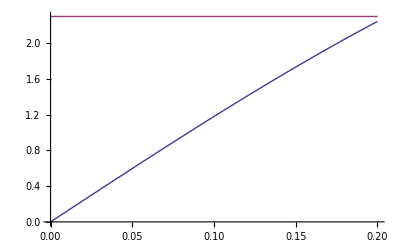

```mathematica
Plot[{Abs[treci[x]],2.3},{x,0,0.2}]
```

```mathematica
m3=Abs[treci[0.2]]
```

2.2444

```mathematica
greska=m3/6 h^2(*ovo je ocena!*)
```

0.00374067

```mathematica
prvi[x_]=D[f[x],x](*ovo je provera, treba da bude manja od ove gore!*)
```

-2 ⅇ^(-x^2) x

```mathematica
Abs[prvi[0.1]-apr]
```

0.00195716

Zadatak 2. Napisati program koji za date tačke x_0-h, x_0 i x_0+h i datu funkciju f izračunava aproksimaciju za f''(x_0) i grešku ovog približnog izračunavanja.

```mathematica
zad2[f_,x_,x0_,h_]:=Module[{},
h1=SetPrecision[h,40];
x0n=SetPrecision[x0,40];
SetPrecision[((f/.x->x0n+h1)-2(f/.x->x0n)+(f/.x->x0n-h1))/h1^2,40]
]
```

```mathematica
zad2[E^(-x^2),x,0.1,0.1]
```

-1.931022834601289763314523773067071166918

```mathematica
Table[zad2[E^(-x^2),x,0.1,10^-k],{k,1,15}]//TableForm
```

-1.93102283460128976436301354547578862297
-1.94040261926706349227527187203606893373
-1.940496723568832682121791699095348461139
-1.940497664642570939051498328631479828167
-1.940497674053311393752499387327075155425
-1.94049767414741879860672264351561160964
-1.940497674148359872655295597402132334588
-1.940497674148369283395781330013130005448
-1.940497674148369377503186187339547195403
-1.940497674148369378444260235912811398024
-1.940497674148369378453670976398544040053
-1.940497674148369378453765083803401366475
-1.940497674148369378453766024877449939737
-1.94049767414836937845376603428819042547
-1.940497674148369378453766034382297830329

```mathematica
greska[f_,x_,x0_,h_]:=Module[{},
drugi=D[f,{x,2}];
ag=Abs[zad2[f,x,x0,h]-drugi/.x->x0];
rg=ag/Abs[drugi/.x->x0];
{ag,rg}
]
greska[E^(-t^2),t,0.1,10^-7]
```

{9.54098×10^-15,4.91677×10^-15}

```mathematica
ocenaGr[f_,x_,x0_,h_,m4_]:=Module[{},
ag=m4/12 h^2;
ap=zad2[f,x,x0,h];
rg=ag/Abs[ap];
{ag,rg}
]
```

```mathematica
cetvrti[x_]=D[E^(-x^2),{x,4}]
```

12 ⅇ^(-x^2)-48 ⅇ^(-x^2) x^2+16 ⅇ^(-x^2) x^4

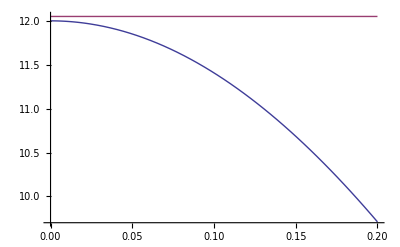

```mathematica
Plot[{Abs[cetvrti[x]],12.05},{x,0,0.2}]
```

```mathematica
m4=Abs[cetvrti[0]]
```

12

```mathematica
ocenaGr[E^(-t^2),t,0.1,10^-7,m4]
```

{1/100000000000000,5.153317179000882698079998778503963296291×10^-15}

Zadatak 3. Napisati program koji za dati skup tačaka, kreira diferencni količnik datog reda (zasnovanog na diferenciranju interpolacionog polinoma date funkcije).

```mathematica
lp[cv_,x_]:=Module[{},
m=Length[cv];
w=1;
Do[
w=w*(x-cv[[i,1]]),
{i,1,m}];
pol=0;
Do[
wi= w/(x-cv[[i,1]]);
pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
{i,1,m}];
pol
]
```

```mathematica
difkol[xlista_,f_,x_,x0_,red_]:=Module[{},
cv=Table[{xlista[[i]],f/.x->xlista[[i]]},{i,1,Length[xlista]}];
pol=lp[cv,x];
izvodRed=D[pol,{x,red}];
izvodRed/.x->x0
]
```

```mathematica
difkol[{x0-h,x0,x0+h},f[x],x,x0,2]//Simplify
```

(-2 f[x0]+f[-h+x0]+f[h+x0])/h^2

```mathematica
difkol[{x0-2h,x0-h,x0,x0+h,x0+2h},f[x],x,x0,2]//Simplify
```

-(30 f[x0]+f[-2 h+x0]-16 f[-h+x0]-16 f[h+x0]+f[2 h+x0])/(12 h^2)

```mathematica
difkol[{x0-2h,x0-h,x0,x0+h,x0+2h},f[x],x,x0,4]//Simplify
```

(6 f[x0]+f[-2 h+x0]-4 f[-h+x0]-4 f[h+x0]+f[2 h+x0])/h^4